```mathematica
(*Mathematica Code for plotting Phase trajectories*)
```

```mathematica
(* F is the dynamical system for the evolutionary dynamics in a static environment*)
(*  SetOptions[EvaluationNotebook[],ShowGroupOpener->True]   *)
```

## Static Environment

### Phase Trajectories

```mathematica
F={
-(4m(m-β)-A(-1+C0)Exp[β/(2m)]M(4m-β)ϕ)/(4 m^2(m-A(-1+C0)Exp[β/(2m)]M*ϕ)),
((1+(C0-1)Exp[β/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(C0-1)Exp[β/(2m)]*M*T*α-m))
}/.{ϕ->α*T};
```

```mathematica
(* params are the parameters of the dynamical system above. The cost of fertilisation here is denoted as C0 instead of C. *)
```

```mathematica
params={A->10,M->10,T->1,C0->0.8,β->1};
```

```mathematica
(*Below we plot numerical solutions to F to plot sample phase trajectories*)
```

```mathematica
nSol1=NDSolve[{
m'[t]==(F[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(F[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.6,
α[0]==0.15
},{m[t],α[t]},{t,0,100}];

nSol2=NDSolve[{
m'[t]==(F[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(F[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.6,
α[0]==0.3
},{m[t],α[t]},{t,0,100}];

nSol3=NDSolve[{
m'[t]==(F[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(F[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.1,
α[0]==0.1
},{m[t],α[t]},{t,0,100}];
```

General::munfl: -4.9×10^7 1.21549929956242×10^-3037 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.93183 (-1.21549929956242×10^-3037) is too small to represent as a normalized machine number; precision may be lost.

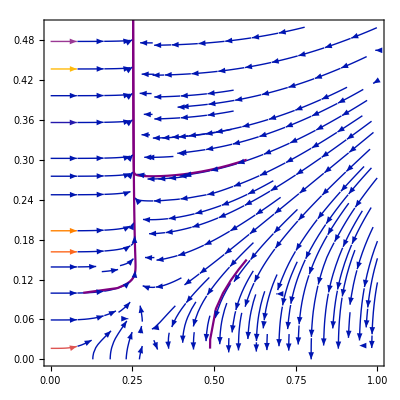

```mathematica
Show[
StreamPlot[F/.params,{m,0,1},{α,0,0.5},StreamStyle->Gray],
ParametricPlot[{m[t],α[t]}/.nSol1,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol2,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol3,{t,0,100},PlotStyle->Purple]]
```

### Deriving Intersection Between Separatrix and m-axis

```mathematica
dαdt=((1+(C0-1)Exp[β/(2*m)])m*Log[1+(A*M*α*T)/m])/(2*α(A(C0-1)Exp[β/(2*m)]M*T*α-m))
```

((1+(-1+C0) ⅇ^(β/(2 m))) m Log[1+(A M T α)/m])/(2 α (-m+A (-1+C0) ⅇ^(β/(2 m)) M T α))

```mathematica
dαdtseries=Series[dαdt,{α,0,1}]
```

-(A (1+(-1+C0) ⅇ^(β/(2 m))) M T)/(2 m)+1/2 (1+(-1+C0) ⅇ^(β/(2 m))) m ((A^2 M^2 T^2)/(2 m^3)-(A^2 (-1+C0) ⅇ^(β/(2 m)) M^2 T^2)/m^3) α+O[α]^2

```mathematica
dαdtseries=Normal[dαdtseries]
```

-(A (1+(-1+C0) ⅇ^(β/(2 m))) M T)/(2 m)+1/2 (1+(-1+C0) ⅇ^(β/(2 m))) m ((A^2 M^2 T^2)/(2 m^3)-(A^2 (-1+C0) ⅇ^(β/(2 m)) M^2 T^2)/m^3) α

```mathematica
Solve[dαdtseries==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→-β/(2 Log[1-C0])}}

## Switching Environment

### Phase Trajectories

```mathematica
(* FSW is the dynamical system for the evolutionary dynamics in a switching environment with fixed time in each environment*)
```

```mathematica
FSW={
-(4m(m-βB)-A(-1+C0)Exp[βB/(2m)]M(4m-βB)ϕ)/(4 m^2(m-A(-1+C0)Exp[βB/(2m)]M*ϕ))*λGB/(λBG+λGB)+-(4m(m-βG)-A(-1+C0)Exp[βG/(2m)]M(4m-βG)ϕ)/(4 m^2(m-A(-1+C0)Exp[βG/(2m)]M*ϕ))*λBG/(λBG+λGB),
((1+(C0-1)Exp[βB/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(C0-1)Exp[βB/(2m)]*M*T*α-m))*λGB/(λBG+λGB)+((1+(C0-1)Exp[βG/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(C0-1)Exp[βG/(2m)]*M*T*α-m))*λBG/(λBG+λGB)
}/.{ϕ->α*T};
```

```mathematica
(* params are the parameters of the dynamical system above. The cost of fertilisation here is denoted as C0 instead of C. *)
```

```mathematica
params={A->10,M->10,T->1,C0->0.3,βB->4, βG->0.002,λGB->1, λBG->2.4};
```

```mathematica
(*Below we plot numerical solutions to F to plot sample phase trajectories*)
```

```mathematica
nSol1SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.5,
α[0]==0.25
},{m[t],α[t]},{t,0,100}];

nSol2SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.1,
α[0]==0.1
},{m[t],α[t]},{t,0,100}];

nSol3SW=NDSolve[{
m'[t]==(FSW[[1]]/.params/.{m->m[t],α->α[t]}),
α'[t]==(FSW[[2]]/.params/.{m->m[t],α->α[t]}),
m[0]==0.2955,
α[0]==0.2254
},{m[t],α[t]},{t,0,100}];
```

General::munfl: -4.9×10^7 2.27282867644836×10^-12158 is too small to represent as a normalized machine number; precision may be lost.

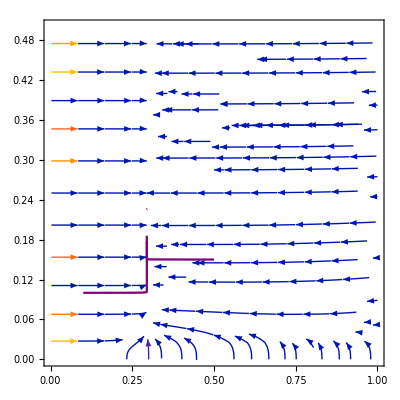

```mathematica
Show[
StreamPlot[FSW/.params,{m,0,1},{α,0,0.5},StreamStyle->Gray],
ParametricPlot[{m[t],α[t]}/.nSol1SW,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol2SW,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol3SW,{t,0,100},PlotStyle->Purple]]
```

### Deriving Switching Induced Fixed Point

```mathematica
(*Here, we solve the first equation of FSW in terms of α to calculate α^{*} *)
params={A->10,M->10,T->1,C0->0.3,βB->4, βG->0.002,λGB->1, λBG->2.4};
```

```mathematica
αstar=Solve[((1+(C0-1)Exp[βB/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(C0-1)Exp[βB/(2m)]*M*T*α-m))*λGB/(λBG+λGB)+((1+(C0-1)Exp[βG/(2m)])m*Log[1+(A*M*α*T)/m])/(2α(A(C0-1)Exp[βG/(2m)]*M*T*α-m))*λBG/(λBG+λGB)==0,α]//FullSimplify;
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
(* Here we approximate the value of m^{*} by taking the limit as ϕ -> infinity, then solving for m*)
```

```mathematica
dmdτϕInf=Limit[-(4m(m-βB)-A(-1+C0)Exp[βB/(2m)]M(4m-βB)ϕ)/(4 m^2(m-A(-1+C0)Exp[βB/(2m)]M*ϕ))*λGB/(λBG+λGB)+-(4m(m-βG)-A(-1+C0)M(4m-βG)ϕ)/(4 m^2(m-A(-1+C0)M*ϕ))*λBG/(λBG+λGB),ϕ->Infinity];
```

```mathematica
mstar=Solve[dmdτϕInf==0,m];
```

```mathematica
(* αstar and mstar is the approximation of the switching induced fixed point *)
```

```mathematica
αstar[[1,1,2]]/.{m->mstar[[1,1,2]]}/.params
```

0.225361

### Checking the Stability of the Switching Induced Fixed Point

```mathematica
a={m,α};
equilib={α->((λBG+(-1+C0) ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) λBG+λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λGB) (βG λBG+βB λGB))/(4 A (-1+C0) M T (λBG+λGB) (ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) λBG+ⅇ^((2 βG (λBG+λGB))/(βG λBG+βB λGB)) (λGB+(-1+C0) ⅇ^((2 βB (λBG+λGB))/(βG λBG+βB λGB)) (λBG+λGB))))/.params, m->(βB λGB+βG λBG)/(4 (λBG+λGB))/.params};
```

```mathematica
j=(D[(FSW/.params),{a}]/.equilib);
```

```mathematica
EigJ=Eigenvalues[j];
```

### Plotting the Switching-Induced Fixed Point

General::munfl: -4.9×10^7 2.27282867644836×10^-12158 is too small to represent as a normalized machine number; precision may be lost.

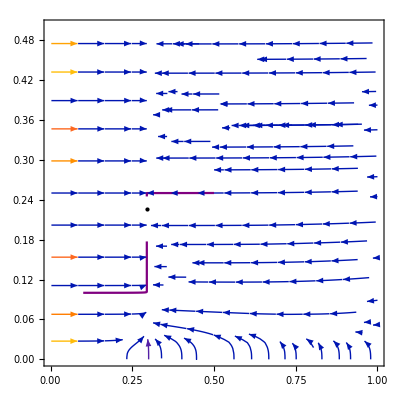

```mathematica
Show[
StreamPlot[FSW/.params,{m,0,1},{α,0,0.5},StreamStyle->Gray],
ParametricPlot[{m[t],α[t]}/.nSol1SW,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol2SW,{t,0,100},PlotStyle->Purple],
ParametricPlot[{m[t],α[t]}/.nSol3SW,{t,0,100},PlotStyle->Purple],
Graphics[{PointSize[Large],Point[{mstar[[1,1,2]]/.params,αstar[[1,1,2]]/.m->mstar[[1,1,2]]/.params}]}]]
```